the rules of chess occupy 10 to the 5 pages in this language.

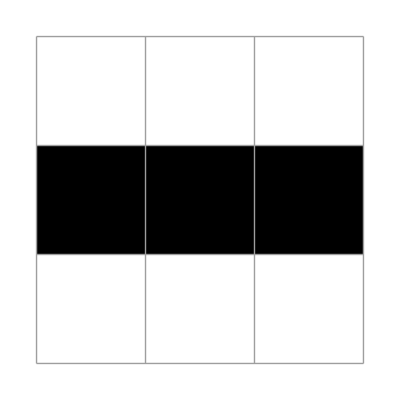
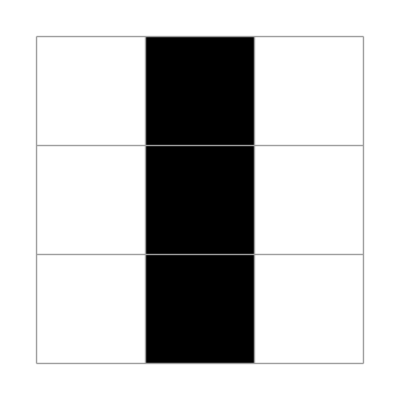

-Graphics-

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Binomial[8,7]
```

8

```mathematica
Not/@Prepend[{1,2,3,4} ,xP]
```

{!xP,!1,!2,!3,!4}

## the 56

```mathematica
Clear[x];
lifeNeighbours={xNW,xN,xNE,xW,xE,xSW,xS,xSE};
lists56stone=Subsets[lifeNeighbours,{3}];
lists56=(Prepend[#,xP])&@((Not/@#)~Join~Complement[lifeNeighbours,#])&/@lists56stone;
the56=And@@Or@@@lists56
```

(xP||!xNW||!xN||!xNE||xE||xS||xSE||xSW||xW)&&(xP||!xNW||!xN||!xW||xE||xNE||xS||xSE||xSW)&&(xP||!xNW||!xN||!xE||xNE||xS||xSE||xSW||xW)&&(xP||!xNW||!xN||!xSW||xE||xNE||xS||xSE||xW)&&(xP||!xNW||!xN||!xS||xE||xNE||xSE||xSW||xW)&&(xP||!xNW||!xN||!xSE||xE||xNE||xS||xSW||xW)&&(xP||!xNW||!xNE||!xW||xE||xN||xS||xSE||xSW)&&(xP||!xNW||!xNE||!xE||xN||xS||xSE||xSW||xW)&&(xP||!xNW||!xNE||!xSW||xE||xN||xS||xSE||xW)&&(xP||!xNW||!xNE||!xS||xE||xN||xSE||xSW||xW)&&(xP||!xNW||!xNE||!xSE||xE||xN||xS||xSW||xW)&&(xP||!xNW||!xW||!xE||xN||xNE||xS||xSE||xSW)&&(xP||!xNW||!xW||!xSW||xE||xN||xNE||xS||xSE)&&(xP||!xNW||!xW||!xS||xE||xN||xNE||xSE||xSW)&&(xP||!xNW||!xW||!xSE||xE||xN||xNE||xS||xSW)&&(xP||!xNW||!xE||!xSW||xN||xNE||xS||xSE||xW)&&(xP||!xNW||!xE||!xS||xN||xNE||xSE||xSW||xW)&&(xP||!xNW||!xE||!xSE||xN||xNE||xS||xSW||xW)&&(xP||!xNW||!xSW||!xS||xE||xN||xNE||xSE||xW)&&(xP||!xNW||!xSW||!xSE||xE||xN||xNE||xS||xW)&&(xP||!xNW||!xS||!xSE||xE||xN||xNE||xSW||xW)&&(xP||!xN||!xNE||!xW||xE||xNW||xS||xSE||xSW)&&(xP||!xN||!xNE||!xE||xNW||xS||xSE||xSW||xW)&&(xP||!xN||!xNE||!xSW||xE||xNW||xS||xSE||xW)&&(xP||!xN||!xNE||!xS||xE||xNW||xSE||xSW||xW)&&(xP||!xN||!xNE||!xSE||xE||xNW||xS||xSW||xW)&&(xP||!xN||!xW||!xE||xNE||xNW||xS||xSE||xSW)&&(xP||!xN||!xW||!xSW||xE||xNE||xNW||xS||xSE)&&(xP||!xN||!xW||!xS||xE||xNE||xNW||xSE||xSW)&&(xP||!xN||!xW||!xSE||xE||xNE||xNW||xS||xSW)&&(xP||!xN||!xE||!xSW||xNE||xNW||xS||xSE||xW)&&(xP||!xN||!xE||!xS||xNE||xNW||xSE||xSW||xW)&&(xP||!xN||!xE||!xSE||xNE||xNW||xS||xSW||xW)&&(xP||!xN||!xSW||!xS||xE||xNE||xNW||xSE||xW)&&(xP||!xN||!xSW||!xSE||xE||xNE||xNW||xS||xW)&&(xP||!xN||!xS||!xSE||xE||xNE||xNW||xSW||xW)&&(xP||!xNE||!xW||!xE||xN||xNW||xS||xSE||xSW)&&(xP||!xNE||!xW||!xSW||xE||xN||xNW||xS||xSE)&&(xP||!xNE||!xW||!xS||xE||xN||xNW||xSE||xSW)&&(xP||!xNE||!xW||!xSE||xE||xN||xNW||xS||xSW)&&(xP||!xNE||!xE||!xSW||xN||xNW||xS||xSE||xW)&&(xP||!xNE||!xE||!xS||xN||xNW||xSE||xSW||xW)&&(xP||!xNE||!xE||!xSE||xN||xNW||xS||xSW||xW)&&(xP||!xNE||!xSW||!xS||xE||xN||xNW||xSE||xW)&&(xP||!xNE||!xSW||!xSE||xE||xN||xNW||xS||xW)&&(xP||!xNE||!xS||!xSE||xE||xN||xNW||xSW||xW)&&(xP||!xW||!xE||!xSW||xN||xNE||xNW||xS||xSE)&&(xP||!xW||!xE||!xS||xN||xNE||xNW||xSE||xSW)&&(xP||!xW||!xE||!xSE||xN||xNE||xNW||xS||xSW)&&(xP||!xW||!xSW||!xS||xE||xN||xNE||xNW||xSE)&&(xP||!xW||!xSW||!xSE||xE||xN||xNE||xNW||xS)&&(xP||!xW||!xS||!xSE||xE||xN||xNE||xNW||xSW)&&(xP||!xE||!xSW||!xS||xN||xNE||xNW||xSE||xW)&&(xP||!xE||!xSW||!xSE||xN||xNE||xNW||xS||xW)&&(xP||!xE||!xS||!xSE||xN||xNE||xNW||xSW||xW)&&(xP||!xSW||!xS||!xSE||xE||xN||xNE||xNW||xW)